# Narciso Cluster Analysis

### Using Mathematica to investigate variations in samples from Porto

## Header

### Standard Header Section

```mathematica
Needs["HierarchicalClustering`"]
Needs["ProteomicsAnalysis`"]
Needs["ManualPCA`"]
Needs["PrincipalComponentsVariance`"]
Needs["VennDiagram`"]
Needs["Sanitized`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\Andrew\Dropbox\shared_AL\Porto_iTRAQ_neutral-sites

```mathematica
FileNames[]
```

{13211_iTRAQ2-pepts.xls,13211_iTRAQ2-quants.xls,13212_iTRAQ1-pepts.xls,13212_iTRAQ1-PHENYX.xls,13212_iTRAQ1-quants.xls,.git,neutral_sites_investigation.nb,porto_iTRAQ1-EASYPROT.xlsx,porto_iTRAQ1_peptide-data.csv,Porto_PCA_iTRAQ1.pdf,Porto_PCA_iTRAQ2.pdf,ProteomicsAnalysis.m,README.md}

## Protein investigation

### Import data

```mathematica
proteins1=Import["13212_iTRAQ1-quants.xls"][[2]];
proteins2=Import["13211_iTRAQ2-quants.xls"][[2]];
proteins1//Dimensions
proteins2//Dimensions
```

{464,66}

{631,66}

### Collect intersecting proteins

```mathematica
acValues1=proteins1[[3;;All,1]];
acValues2=proteins2[[3;;All,1]];
```

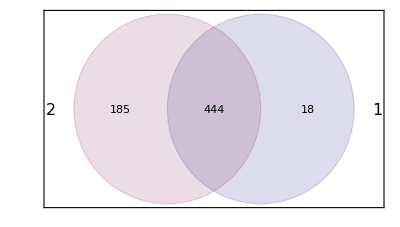

```mathematica
VennDiagram[{acValues1,acValues2}]
```

```mathematica
sharedProteins=Intersection[acValues1,acValues2];
Dimensions[sharedProteins]
```

{444}

### PCA of intersecting proteins

```mathematica
proteinIntensities1=Map[Association@@Thread[acValues1->#]&,proteins1[[3;;All,27;;34]]ᵀ]; (*Isotopic correction, Median correction, Log Values*)
proteinIntensities2=Map[Association@@Thread[acValues2->#]&,proteins2[[3;;All,27;;34]]ᵀ];
```

```mathematica
sharedProteinIntensities=Table[f[[All,Key[sharedProteins[[k]]]]],{k,Length[sharedProteins]},{f,{proteinIntensities1,proteinIntensities2}}];
sharedProteinIntensities=Flatten[Transpose[sharedProteinIntensities,{3,1,2}],1]ᵀ;
```

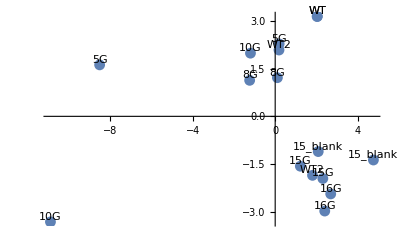

```mathematica
labels={"WT","WT2","15G","15G","16G","16G","15_blank","15_blank","WT","WT2","5G","5G","8G","8G","10G","10G"};
pca=PrincipalComponents[sharedProteinIntensitiesᵀ];
ListPlot[pca[[All,1;;2]],Epilog->Table[Text[labels[[i]],pca[[i,{1,2}]],{0,-2}],{i,16}],PlotRangePadding->Scaled[.1],PlotRange->Full]
```

Not meshing properly based on WT2 positioning.

## Peptide investigation

### Import data

```mathematica
rawPeptideData1=Import["13212_iTRAQ1-pepts.xls"][[1]];
rawPeptideData2=Import["13211_iTRAQ2-pepts.xls"][[1]];
Dimensions[rawPeptideData1]
Dimensions[rawPeptideData2]
```

{8000,20}

{14815,20}

### Putting the data into a workable format

```mathematica
heads=rawPeptideData1[[1,All]];
workingPeptideData1=rawPeptideData1[[2;;All,All]];
workingPeptideData2=rawPeptideData2[[2;;All,All]];
```

```mathematica
heads[[11;;18]]
labelIntensities1=workingPeptideData1[[All,11;;18]];
labelIntensities2=workingPeptideData2[[All,11;;18]];
```

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

### Removing empty rows and null intensity data

```mathematica
labelIntensities1=labelIntensities1/.""->0.;
labelIntensities2=labelIntensities2/.""->0.;
```

### Mapping associations ???

```mathematica
(* -- Failed Analysis --
a1=Map[Association@@Thread[workingPeptideData1[[All,2]]->#]&,sanitisedPeptides1ᵀ];
a2=Map[AssociationThread[workingPeptideData2[[All,2]]->#]&,sanitisedPeptides2ᵀ];
*)
```

```mathematica
labelIntensities1=Map[AssociationThread[heads[[11;;18]]->#]&,labelIntensities1];
labelIntensities2=Map[AssociationThread[heads[[11;;18]]->#]&,labelIntensities2];
c1=labelIntensities1;
c2=labelIntensities2;(*For comparison*)
```

### Normalising the data

#### By channel sum

```mathematica
a1=Table[
(100000/Total[#[[All,i]]])*#[[All,i]],{i,8}]ᵀ;&[labelIntensities1]
a1=Map[AssociationThread[heads[[11;;18]]->#]&,a1];

a2=Table[
(100000/Total[#[[All,i]]])*#[[All,i]],{i,8}]ᵀ;&[labelIntensities2]
a2=Map[AssociationThread[heads[[11;;18]]->#]&,a2];
```

```mathematica
labelIntensities1[[1]]
a1[[1]]
```

<|113.1→0.5546,114.1→0.5856,115.1→0.5499,116.1→0.8452,117.1→0.791,118.1→0.6297,119.1→0.6373,121.1→0.6327|>

<|113.1→0.806501,114.1→0.95593,115.1→0.971687,116.1→1.23677,117.1→1.18442,118.1→1.19918,119.1→1.10602,121.1→1.17583|>

#### By median correction

This should be a function, it’s failing for arbitrary reasons. Doesn’t like the loop for determining the quartiles for some reasons.

```mathematica
(*
medianCorrection[data_]:=Association@@Table[
log=Log[data⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
log=N[log]/.-∞->min;
{L,M,R}=Evaluate[Quantile[log,{0.4,0.5,0.6}]];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}]
*)
```

```mathematica
b1=c1;
normalised=Association@@Table[
log=Log[#⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
{L,M,R}=Quantile[log,{0.4,0.5,0.6}];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}];&[b1]
Do[b1⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,heads[[11;;18]]}]
```

```mathematica
b2=c2;
normalised=Association@@Table[
log=Log[#⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
{L,M,R}=Quantile[log,{0.4,0.5,0.6}];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}];&[b2]
Do[b2⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,heads[[11;;18]]}]
```

#### Graphs

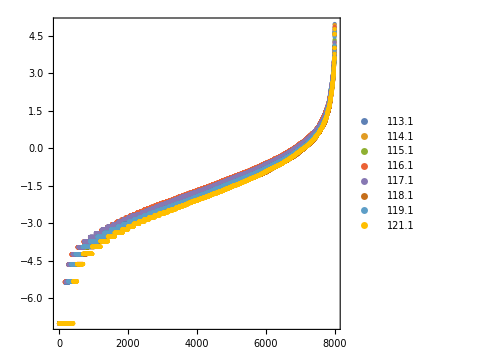
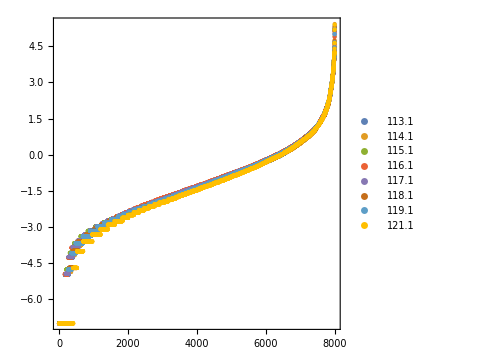
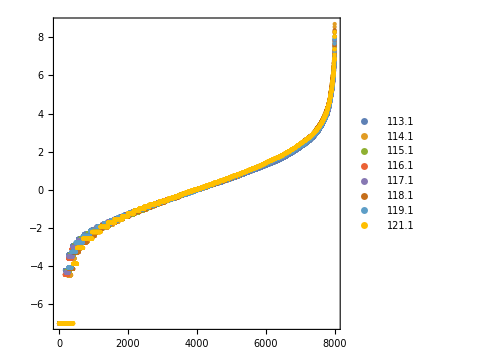
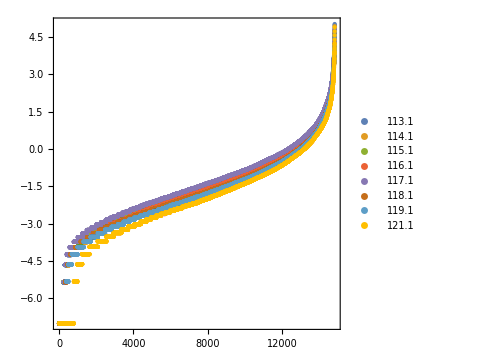
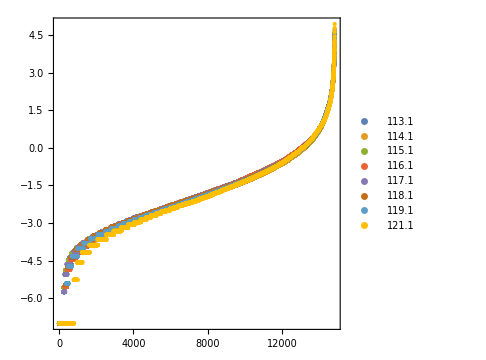
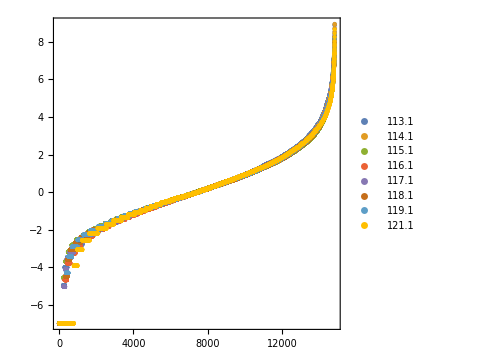

```mathematica
graphs=Table[ListPlot[Evaluate@Table[Sort[N[Log[#⟦All,Key[k]⟧/.(0|0.->Exp[-7.])]]],{k,heads[[11;;18]]}],
PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,
PlotLegends->heads[[11;;18]],PlotStyle->PointSize[Medium]]&[i],{i,{c1,a1,b1,c2,a2,b2}}]
```

### Quants

```mathematica
workingPeptideData1[[All,11;;18]]/.//Dimensions
```

{7999,8}

#### From Joss

```mathematica
dat1=Map[Association@@Thread[heads->#]&,workingPeptideData1];
gdat1=GatherBy[dat1,#AC&];
gdat1=Select[gdat1,Length[#]≥3&];
gdat1=Select[gdat1,Length[Union[#⟦All,"sequence"⟧]]≥2&];
dat2=Map[Association@@Thread[heads->#]&,workingPeptideData2];
gdat2=GatherBy[dat2,#AC&];
gdat2=Select[gdat2,Length[#]≥3&];
gdat2=Select[gdat2,Length[Union[#⟦All,"sequence"⟧]]≥2&];
```

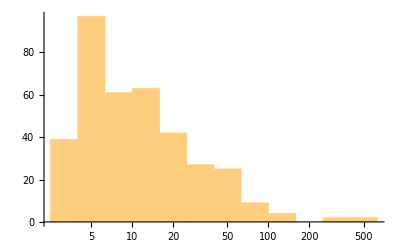

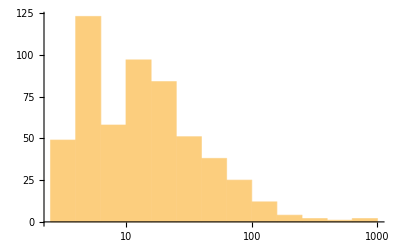

```mathematica
Histogram[Length/@gdat1,"Log"]
Histogram[Length/@gdat2,"Log"]
```

```mathematica
flatSharedPeptides1=Flatten[gdat1];
flatSharedPeptides2=Flatten[gdat2];
```

```mathematica
sharedProteins=Intersection[flatSharedPeptides1[[All,2]],flatSharedPeptides2[[All,2]]];
%//Length
```

365

```mathematica
labels=heads[[11;;18]]
```

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

```mathematica
Values@gdat1[[1]]//Dimensions
```

{113,20}

```mathematica
quants=Table[Association@Thread[labels->GeometricMean/@Transpose[Values@gdat1⟦i,All,Key/@labels⟧]],{i,Length[gdat1]}];
quants⟦1⟧
```

<|113.1→0.278655 (^2)^(1/113),114.1→0.259283 (^2)^(1/113),115.1→0.246142 ^(1/113),116.1→0.340004 (^2)^(1/113),117.1→0.326899 (^2)^(1/113),118.1→0.242355 (^5)^(1/113),119.1→0.242115 (^3)^(1/113),121.1→0.252851 (^4)^(1/113)|>

```mathematica
Values@quants//Dimensions
```

{371,8}

```mathematica
quants=Map[#/GeometricMean[{#⟦Key[114.1]⟧,#⟦Key[115.1]⟧}]&,quants];
```

```mathematica
quants=Table[GeometricMean/@gdat1⟦i,All,j⟧,{i,Length[gdat1]},{j,11,18}];
```

GeometricMean::vecmat1: Argument 0.5546 is neither a non-empty vector nor a non-empty matrix.

GeometricMean::vecmat1: Argument 1.1091 is neither a non-empty vector nor a non-empty matrix.

GeometricMean::vecmat1: Argument 1.0096 is neither a non-empty vector nor a non-empty matrix.

General::stop: Further output of GeometricMean :: vecmat1 will be suppressed during this calculation.

```mathematica
GeometricMean[gdat1[[1,All,11]]]
```

0.278655 (^2)^(1/113)

```mathematica
GeometricMean[gdat1⟦1,All,Key/@labels[[1]]⟧]
quants⟦1⟧
```

Part::pkspec1: The expression 113.1 cannot be used as a part specification.

GeometricMean::vecmat1: Argument {{<| "jobid" → 13212., "AC" → "M1LID4", "sequence" → "SALDEIVLVGGSTR", "charge" → 2., "zscore" → 13.776, "pvalue" → 1.245×10^-41, "is selected" → 1., "moz" → 860.989, "miss. cleav." → 0., "modif" → "iTRAQ_8plex_Nterm:::::::::::::::", 113.1 → 0.5546, 114.1 → 0.5856, 115.1 → 0.5499, 116.1 → 0.8452, 117.1 → 0.791, 118.1 → 0.6297, 119.1 → 0.6373, 121.1 → 0.6327, "spectra descr." → "File: FIL_ITRAQ1_F70_02.wiff, Sample: FIL_ITRAQ1_F70_02 (sample number 1), Elution: 70.044 to 71.048 min, Period: 1, Cycle(s): 2713, 2724 (Experiment 2)", "pm key" → "SALDEIVLVGGSTR%iTRAQ_8plex_Nterm:::::::::::::::%sample_0%cmpd_12235" |>, « 49 », « 63 »}, {« 1 »}, {« 1 »}, {<| « 1 » |>, <| « 1 » |>, <| « 1 » |>, « 46 », <| « 1 » |>, « 16 »}, « 44 », {« 1 »}, {« 1 »}, « 321 »} ⟦ « 1 » ⟧ is neither a non-empty vector nor a non-empty matrix.

### Cluster Analysis

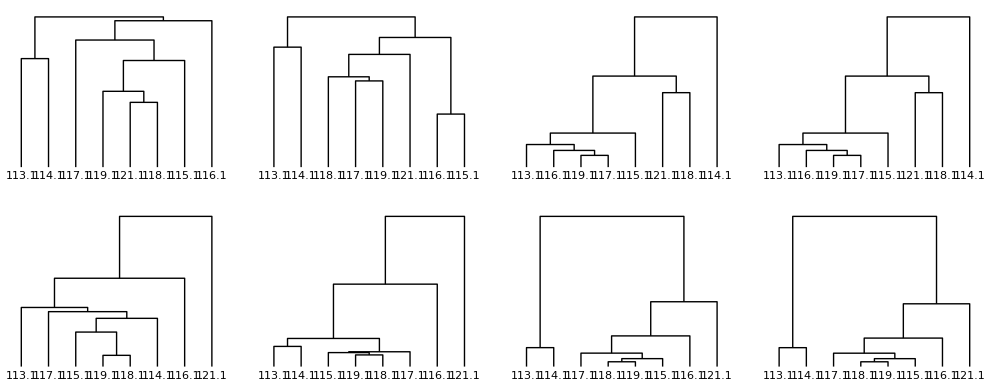

```mathematica
GraphicsGrid[{
{"","Unnormalised","Channel-sum correction","Median correction","Shared proteins only"},
{"iTRAQ1",
DendrogramPlot[Values@c1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@a1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@b1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@flatSharedPeptides1ᵀ,LeafLabels->heads[[11;;18]]]},
{"iTRAQ2",
DendrogramPlot[Values@c2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@a2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@b2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@flatSharedPeptides2ᵀ,LeafLabels->heads[[11;;18]]]
}}]
```

### PCA

```mathematica
pca1a=PrincipalComponents[normalisedPeptides1ᵀ];
pca1b=PrincipalComponents[Values@b1ᵀ];
pca2a=PrincipalComponents[normalisedPeptides2ᵀ];
pca2b=PrincipalComponents[Values@b2ᵀ];
```

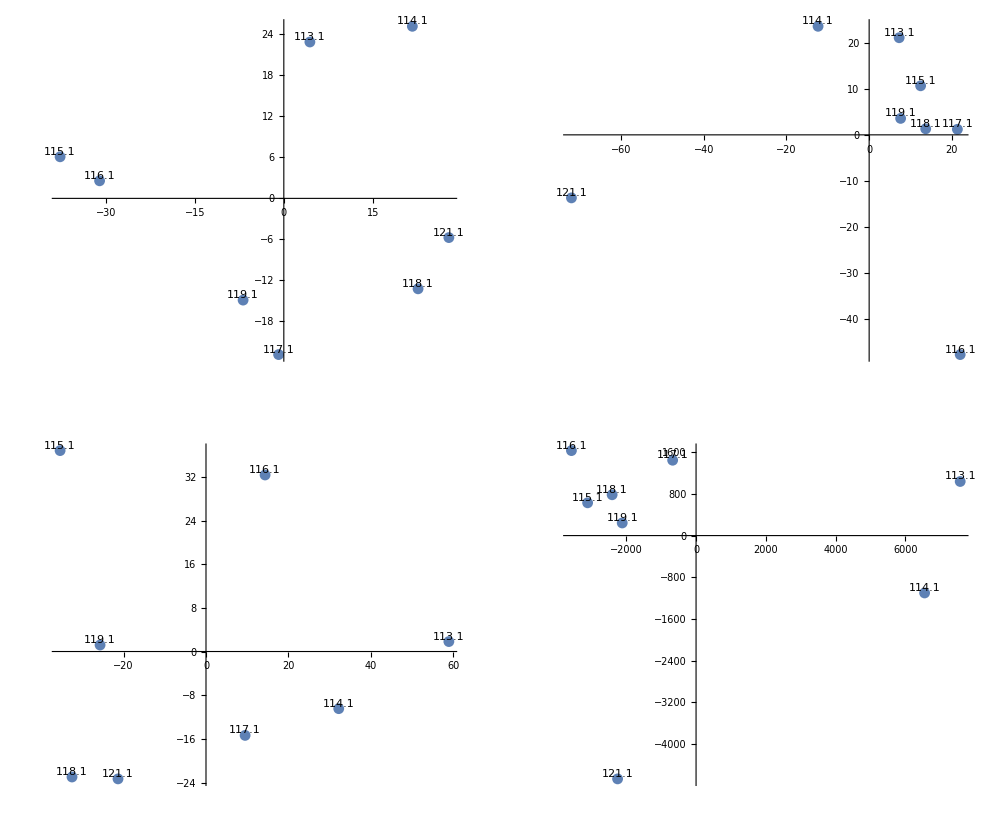

```mathematica
GraphicsGrid[{{"","iTRAQ1","iTRAQ2"},
{"ChannelSum",pcaPlot1a=ListPlot[pca1a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]],
pcaPlot2a=ListPlot[pca2a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]},
{"MedianCorrect",pcaPlot1b=ListPlot[pca1b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]],
pcaPlot2b=ListPlot[pca2b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]}}]
```

```mathematica
Export["Porto_PCA_iTRAQ1.pdf",pcaPlot1]
Export["Porto_PCA_iTRAQ2.pdf",pcaPlot2]
```